# Analytical results of chapter 4

# c = 1 and ω = 1

```mathematica
c = 1;
ω = 1;
```

```mathematica
θA= θ;
θB = θ;
νA = FullSimplify[(c (-2-μ (5+2 μ+R0 (-1+ω)+(2+μ) (1+2 μ) ω))+(1+μ) (2+μ (2+(3+2 μ) ω)))/(c (-1+R0) (2+μ (3+2 μ)) (1+μ ω))];
νB =FullSimplify[(-((1+μ) (2+μ ω) (1+2 μ ω))+c (2+μ (3+R0 (-1+ω)+ω (4+5 μ+2 μ (1+μ) ω))))/((-1+c R0) (1+μ) (2+μ ω (3+2 μ ω)))];
```

## With antisymmetric fitness

```mathematica
λ12 = -t*x;
λ21 = t*x;
ι12 = x;
ι21 = -x;
```

```mathematica
eqA = θA*zA*(λ12(1-zA) -(λ12 + λ21)zA(1-zA)) + d*(νA - 1)(zA - zB)
eqB = θB*zB*(ι12(1-zB) - (ι12 + ι21)zB(1-zB)) + d*(νB -1)(zB-zA)
```

-d (zA-zB)-t x (1-zA) zA θ

-d (-zA+zB)+x (1-zB) zB θ

```mathematica
eq = FullSimplify[Solve[{eqA == 0, eqB == 0}, {zA, zB}]]
```

{{zA→0,zB→0},{zA→1,zB→1},{zA→(2 d+t x θ-√t √(4 d^2+t x^2 θ^2))/(2 t x θ),zB→-(2 d-x θ-(√(4 d^2+t x^2 θ^2))/(√t))/(2 x θ)},{zA→(2 d+t x θ+√t √(4 d^2+t x^2 θ^2))/(2 t x θ),zB→-(2 d-x θ+(√(4 d^2+t x^2 θ^2))/(√t))/(2 x θ)}}

Only one of the two coex equilibria is feasible:

```mathematica
ParamRange = d > 0 && θ > 0 && t > 0 && x > 0;
```

```mathematica
coexExists = Reduce[0< {zA/.eq[[3]]} < 1 &&0< {zB/.eq[[3]]} < 1 && ParamRange]
```

θ>0&&d>0&&((0<x<d/θ&&d/(d+x θ)<t<d/(d-x θ))||(x≥d/θ&&t>d/(d+x θ)))

```mathematica
FullSimplify[%]
```

θ>0&&d>0&&t>d/(d+x θ)&&((x>0&&t<d/(d-x θ))||d/θ≤x)

```mathematica
Reduce[0<= {zA/.eq[[4]]} <= 1 &&0<= {zB/.eq[[4]]} <= 1 && ParamRange]
```

False

```mathematica
coexEq = eq[[3]]
```

{zA→(2 d+t x θ-√t √(4 d^2+t x^2 θ^2))/(2 t x θ),zB→-(2 d-x θ-(√(4 d^2+t x^2 θ^2))/(√t))/(2 x θ)}

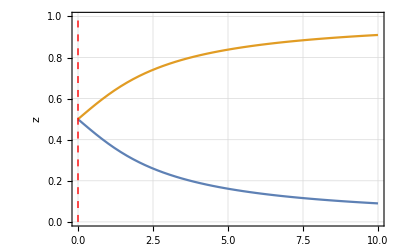

```mathematica
m = 1;
μ  = 0.5;
Θ= 2m/(2μ^2 + 3μ  + 2);
t = 1;
d = 0.5;
zAstar =  0.5 + d/(t*x*Θ) - Sqrt[t(4*d^2 + t*x^2*Θ^2)]/(2t*x*Θ);
zBstar  =  0.5 - d/(x*Θ) + Sqrt[t(4*d^2 + t*x^2*Θ^2)]/(2t*x*Θ);
tresh = Abs[(d-d*t)/(t*Θ)];
line = Line[{{tresh, 0}, {tresh, 1}}];

Plot[{zAstar/. {x -> X }, {zBstar/.{x -> X}}}, {X, 0, 10}, PlotRange ->{0, 1}, PlotTheme->"Detailed", PlotLegends->{"", ""},FrameLabel->{"", "z"},  Epilog->{ Directive[Thick, Red, Dashed], line, Directive[Black],Text["", {tresh +1, 0.8} ]}, PlotTheme->"Scientific"]
```

```mathematica
Clear[m, μ, Θ, t, d]
```

Meaning that only the first coex point is feasible and exists for those regions relating x, t, d an θ. The second coex point is never inside the feasible range.

Lets look at stability:

```mathematica
Jac = {{D[eqA, zA], D[eqA, zB]}, {D[eqB, zA], D[eqB, zB]}};
```

```mathematica
Jac00 = Jac/.{zA-> 0, zB-> 0};
Jac11 = Jac/.{zA-> 1, zB-> 1};
JacC = Jac/.eq[[3]];
```

## (0, 0) is stable if:

```mathematica
stable00 = Reduce[Tr[Jac00] < 0 && Det[Jac00] > 0 && ParamRange]
```

d>0&&x>0&&t>1&&0<θ<(-d+d t)/(t x)

## (1, 1) is stable if:

```mathematica
stable11 = Reduce[Tr[Jac11] < 0 && Det[Jac11] > 0 && ParamRange]
```

d>0&&x>0&&0<t<1&&0<θ<(d-d t)/(t x)

## Coex is stable if:

```mathematica
stableC = Reduce[Tr[JacC] < 0 && Det[JacC] > 0 && ParamRange]
```

θ>0&&((0<t≤1&&d>0&&x>(d-d t)/(t θ))||(t>1&&d>0&&x>(-d+d t)/(t θ)))

```mathematica
E1 = FullSimplify[stable11 && Not[stable00]]
```

t>0&&θ>0&&x>0&&t<1&&t (d+x θ)<d

```mathematica
E2 = FullSimplify[Not[stable11]&&stable00]
```

t>1&&θ>0&&x>0&&d t>d+t x θ

```mathematica
Coex = FullSimplify[Not[stable11]&& Not[stable00]]
```

((θ≥(d (-1+t))/(t x)||t≤1)&&(t≤0||t≥1||(d (-1+t))/(t x)+θ≥0))||θ≤0||d≤0||x≤0

```mathematica
Bistable= FullSimplify[stable11&& stable00]
```

False

## Without anti-symmetric fitness

```mathematica
Clear[λ12, λ21, ι12, ι21]
```

```mathematica
eqA = θA*zA*(λ12(1-zA) -(λ12 + λ21)zA(1-zA)) + d*(νA - 1)(zA - zB)
eqB = θB*zB*(ι12(1-zB) - (ι12 + ι21)zB(1-zB)) + d*(νB -1)(zB-zA)
```

-d (zA-zB)+zA θ ((1-zA) λ12-(1-zA) zA (λ12+λ21))

-d (-zA+zB)+zB θ ((1-zB) ι12-(1-zB) zB (ι12+ι21))

```mathematica
eq = FullSimplify[Solve[{eqA == 0, eqB == 0}, {zA, zB}]]
```

No closed form expression for coexistence

```mathematica
ParamRange = d > 0 && θ > 0  && λ12 < 0 && λ21 > 0 && ι12 > 0 && ι21 < 0;
```

Lets look at stability:

```mathematica
Jac = {{D[eqA, zA], D[eqA, zB]}, {D[eqB, zA], D[eqB, zB]}};
```

```mathematica
Jac00 = Jac/.{zA-> 0, zB-> 0};
Jac11 = Jac/.{zA-> 1, zB-> 1};
```

## (0, 0) is stable if:

```mathematica
stable00 = Reduce[Tr[Jac00] < 0 && Det[Jac00] > 0 && ParamRange]
```

λ21>0&&d>0&&λ12<0&&0<ι12<-λ12&&0<θ<(d ι12+d λ12)/(ι12 λ12)&&ι21<0

## (1, 1) is stable if:

```mathematica
stable11 = Reduce[Tr[Jac11] < 0 && Det[Jac11] > 0 && ParamRange]
```

λ12<0&&ι12>0&&d>0&&λ21>0&&ι21<-λ21&&0<θ<(d ι21+d λ21)/(ι21 λ21)

# c >1

```mathematica
Clear[c, νA, νB]
```

```mathematica
ω = 1;
```

```mathematica
θA= θ;
θB = θ;
```

## With antisymmetric fitness

```mathematica
λ12 = -t*x;
λ21 = t*x;
ι12 = x;
ι21 = -x;
```

```mathematica
eqA = θA*zA*(λ12(1-zA) -(λ12 + λ21)zA(1-zA)) + d*(νA - 1)(zA - zB)
eqB = θB*zB*(ι12(1-zB) - (ι12 + ι21)zB(1-zB)) + d*(νB -1)(zB-zA)
```

-t x (1-zA) zA θ+d (zA-zB) (-1+νA)

x (1-zB) zB θ+d (-zA+zB) (-1+νB)

```mathematica
eq = FullSimplify[Solve[{eqA == 0, eqB == 0}, {zA, zB}]]
```

{{zA→0,zB→0},{zA→1,zB→1},{zA→(t x θ-2 d (-1+νA)-√t √(t x^2 θ^2+4 d^2 (-1+νA) (-1+νB)))/(2 t x θ),zB→1/2 (1+(√(t x^2 θ^2+4 d^2 (-1+νA) (-1+νB))+2 d √t (-1+νB))/(√t x θ))},{zA→(t x θ-2 d (-1+νA)+√t √(t x^2 θ^2+4 d^2 (-1+νA) (-1+νB)))/(2 t x θ),zB→1/2-(√(t x^2 θ^2+4 d^2 (-1+νA) (-1+νB)))/(2 √t x θ)+(d (-1+νB))/(x θ)}}

Only one of the two coex equilibria is feasible:

```mathematica
ParamRange = d > 0 && θ > 0  &&x > 0 && t > 0&& c> 1 ;
```

```mathematica
Reduce[0<= {zA/.eq[[3]]} <= 1 &&0<= {zB/.eq[[3]]} <= 1 && ParamRange && νA <1 && νB <1]
```

c>1&&νB<1&&θ>0&&x>0&&((0<d≤-(x θ)/(-1+νB)&&νA<1&&t≥(-d+d νA)/(-d-x θ+d νB))||(d>-(x θ)/(-1+νB)&&νA<1&&(-d+d νA)/(-d-x θ+d νB)≤t≤(-d+d νA)/(-d+x θ+d νB)))

```mathematica
Reduce[0<= {zA/.eq[[4]]} <= 1 &&0<= {zB/.eq[[4]]} <= 1 && ParamRange&&νA <1 && νB <1]
```

False

Meaning that only the first coex point is feasible and exists for those regions relating x, t, d an θ. The second coex point is never inside the feasible range.

Lets look at stability:

```mathematica
Jac = {{D[eqA, zA], D[eqA, zB]}, {D[eqB, zA], D[eqB, zB]}};
```

```mathematica
Jac00 = Jac/.{zA-> 0, zB-> 0};
Jac11 = Jac/.{zA-> 1, zB-> 1};
Jac00 //MatrixForm
Jac11//MatrixForm
```

(-t x θ+d (-1+νA) | -d (-1+νA)
-d (-1+νB) | x θ+d (-1+νB))

(t x θ+d (-1+νA) | -d (-1+νA)
-d (-1+νB) | -x θ+d (-1+νB))

## (0, 0) is stable if:

```mathematica
stable00 = FullSimplify[Reduce[Tr[Jac00] < 0 && Det[Jac00] > 0 && ParamRange]]
```

d>0&&x>0&&t>0&&θ>0&&d (1+t) (x θ+d (1+t) (-1+νB))<0&&1+t (-1+(x θ)/d+νB)<νA&&νA+νB<2+((-1+t) x θ)/d&&c>1

## (1, 1) is stable if:

```mathematica
stable11 = Reduce[Tr[Jac11] < 0 && Det[Jac11] > 0 && ParamRange]
```

d>0&&x>0&&t>0&&θ>0&&c>1&&((νB≤(d+d t+x θ)/(d+d t)&&νA<(d-d t-t x θ+d t νB)/d)||(νB>(d+d t+x θ)/(d+d t)&&νA<(2 d+x θ-t x θ-d νB)/d))

```mathematica
E1 = FullSimplify[stable11 && Not[stable00]]
```

d>0&&x>0&&t>0&&θ>0&&c>1&&((1+(x θ)/(d+d t)≥νB&&t+(t x θ)/d+νA<1+t νB)||(νB>1+(x θ)/(d+d t)&&((-1+t) x θ)/d+νA+νB<2))&&(d (1+t) (x θ+d (1+t) (-1+νB))≥0||νA+νB≥2+((-1+t) x θ)/d||1+t (-1+(x θ)/d+νB)≥νA)

```mathematica
E2 = FullSimplify[Not[stable11]&&stable00]
```

d (-2+νA+νB)<(-1+t) x θ&&d+t x θ+d t νB<d (t+νA)&&x θ+d (1+t) (-1+νB)<0&&c>1&&d>0&&t>0&&x>0&&θ>0

```mathematica
Coex = FullSimplify[Not[stable11]&& Not[stable00]]
```

((t+(t x θ)/d+νA≥1+t νB||νB>1+(x θ)/(d+d t))&&(d (1+t) (x θ+d (1+t) (-1+νB))≥0||νA+νB≥2+((-1+t) x θ)/d||1+t (-1+(x θ)/d+νB)≥νA)&&(((-1+t) x θ)/d+νA+νB≥2||νB≤1+(x θ)/(d+d t)))||c≤1||d≤0||t≤0||x≤0||θ≤0

```mathematica
Bistable= FullSimplify[stable11&& stable00]
```

False